```mathematica
SetDirectory[NotebookDirectory[]];
```

## Import Data

```mathematica
dataCFG2021=Import["data\\PruningSelfEsteem01072021.csv"];
dataCFG2021[[1]]=StringDelete[First@dataCFG2021,"\r\n"];
dataCFG2021=AssociationThread[First@dataCFG2021,#]&/@Rest@dataCFG2021//Dataset;
```

```mathematica
dataCFG2020=Import["data\\PruningHUJI30082021.csv"];
dataCFG2020[[1]]=StringDelete[First@dataCFG2020,"\r\n"];
dataCFG2020=AssociationThread[First@dataCFG2020,#]&/@Rest@dataCFG2020//Dataset;
```

```mathematica
dataTTT2021=Import["data\\huji2_agg_02072021.csv"];
dataTTT2021[[2;;,2]]=N@(dataTTT2021[[2;;,2]]/1000);
dataTTT2021=AssociationThread[First@dataTTT2021,#]&/@Rest@dataTTT2021//Dataset;
```

```mathematica
dataTTT2020=Import["data\\huji_agg_ttt_19102020.csv"];
dataTTT2020=AssociationThread[First@dataTTT2020,#]&/@Rest@dataTTT2020//Dataset;
```

```mathematica
data2021=JoinAcross[dataCFG2021,dataTTT2021,"ID"->"userid"];
data2020=JoinAcross[dataCFG2020,dataTTT2020,"ID"->"userid"];
data=Join[data2021,data2020];
labels=data//Keys//Normal//First
```

{ID,Date/Time,Total Play Time,Total # moves,Average Speed,galleries#,self avoidance,clusters#,% shapes in exp,% time in exp,exp optimality,scav optimality,optimalityratio,median # steps between shapes in exp,median # steps between shapes in scav,expspeed,scavspeed,Orig,Orig (united),Orig exp,Orig exp (united),Orig scav,Orig scav (united),Orig trans,Orig trans (united),Unique Shapes,Unique Shapes exp,Unique Shapes scav,# clusters in GC,% clusters in GC,max Δt (min),userid,time_solution,num_actions,solved_correct,verified_correct,mean_time_from_action,median_time_from_action,var_time_from_action,number_of_paths,shutter_mean,shutter_median,shutter_var,x_misses,o_misses,entropy,density,linear,non-linear,interaction,blocking,participants_log_likelihoods,mean_exploration_times,mean_exploitation_times,median_exploration_times,median_exploitation_times,var_exploration_times,var_exploitation_times,mean_exploitation_actions,median_exploitation_actions,var_exploitation_actions,explore_exploit_time_correlations,explore_time_exploit_actions_correlations,explore_time_exploit_time_between_actions_correlations,mean_thinking_time_exploitation,x_o_exploitation_times_ratios,x_o_exploitation_unforced_times_ratios,shutter_zero_percent,same_starting_point_percent,first_moves_entropy,distances_first_moves_next_path,distances_first_moves_next_path_zero_percent}

```mathematica
data//Length
```

125

## Exclusion Criteria

```mathematica
maxΔtCFG=1.5;
minActionsTTT=5;
minTimeCFG = 600;
minActionsCFG=80;
```

```mathematica
ids=Normal@data[[;;,"ID"]];
```

```mathematica
(data=Select[data,#"max Δt (min)"<maxΔtCFG&])//Length
Print["removed: ",ids~Complement~(ids=Normal@data[[;;,"ID"]])]
```

122

removed: {422893,7894069,8583348}

```mathematica
(data=Select[data,#"num_actions"≥minActionsTTT&])//Length
Print["removed: ",ids~Complement~(ids=Normal@data[[;;,"ID"]])]
```

120

removed: {706080,9608752}

```mathematica
(data=Select[data,#"Total Play Time"≥minTimeCFG&])//Length
Print["removed: ",ids~Complement~(ids=Normal@data[[;;,"ID"]])]
```

120

removed: {}

```mathematica
(data=Select[data, #"Total # moves"≥minActionsCFG&])//Length
Print["removed: ",ids~Complement~(ids=Normal@data[[;;,"ID"]])]
```

120

removed: {}

```mathematica
(* remove participants after the date we opened the study for money *)
(data=Select[data,ToExpression@Normal@#[["Date/Time"]]<DateObject[{2021,5,25,0,0,0}]&])//Length
```

103

## Variables Distribution & Outliers

```mathematica
outliers={};
```

### CFG

#### Median Exploration Steps

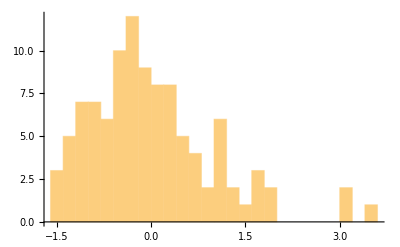

```mathematica
Histogram[#,16]&@Standardize@Normal@data[[;;,"median # steps between shapes in exp"]]
```

```mathematica
MinMax@Standardize@Normal@data[[;;,"median # steps between shapes in exp"]]
```

{-1.4317,3.51399}

```mathematica
Length@Select[ReverseSort@Standardize@Normal@data[[;;,"median # steps between shapes in exp"]],#>3&]
```

3

```mathematica
ReverseSortBy[data,#"median # steps between shapes in exp"&][[;;%,"ID"]]
```

Dataset[<>]

```mathematica
outliers=outliers∪%
```

{3679849,8326152,9600597}

#### Median Exploitation Steps

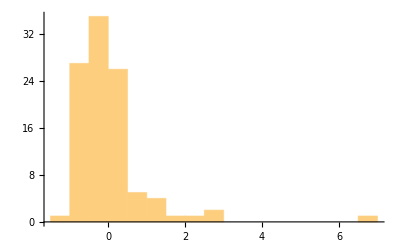

```mathematica
Histogram[#,16,PlotRange->All]&@Standardize@Normal@data[[;;,"median # steps between shapes in scav"]]
```

```mathematica
MinMax@Standardize@Normal@data[[;;,"median # steps between shapes in scav"]]
```

{-1.25429,6.82835}

```mathematica
Length@Select[ReverseSort@Standardize@Normal@data[[;;,"median # steps between shapes in scav"]],#>3&]
```

1

```mathematica
ReverseSortBy[data,#"median # steps between shapes in exp"&][[;;%,"ID"]]
```

Dataset[<>]

```mathematica
outliers=outliers∪%
```

{3679849,8326152,9600597}

### TTT

#### participants_log_likelihood

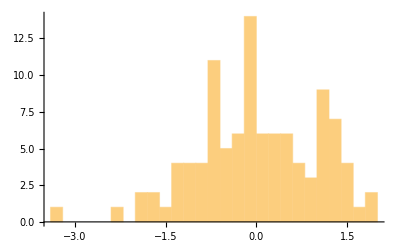

```mathematica
Histogram[#,16]&@Standardize@Normal@data[[;;,"participants_log_likelihoods"]]
```

```mathematica
MinMax@Standardize@Normal@data[[;;,"participants_log_likelihoods"]]
```

{-3.24559,1.92016}

```mathematica
Length@Select[Sort@Standardize@Normal@data[[;;,"participants_log_likelihoods"]],#<-3&]
```

1

```mathematica
MinimalBy[data,#"participants_log_likelihoods"&][[;;,"ID"]]
```

Dataset[<>]

```mathematica
outliers=outliers∪%
```

{3679849,5221452,8326152,9600597}

### Drop outliers

```mathematica
outliers
```

{3679849,5221452,8326152,9600597}

```mathematica
(data=Select[data,!MemberQ[outliers,#"ID"]&])//Length
```

99

## Forcing log likelihood-ratio

```mathematica
LLRForcing=Normal@Values@data[[;;,47;;50]]-Normal@data[[;;,51]]
```

{{-1.28368,-0.547785,-0.217887,-0.0944041},{-0.519325,0.263619,0.301807,0.0438625},{-1.56226,-0.679173,-0.354012,-0.0849898},{0.536368,0.457445,0.419486,0.0711325},{-2.18648,-0.681691,-0.425956,-0.204433},{-0.520151,0.286469,0.268699,0.10646},{-0.545029,-0.0638362,0.0860176,-0.0289041},{-1.76246,-0.819893,-0.451342,-0.0841267},{-1.25621,-0.575047,-0.313267,-0.185761},{-1.95947,-1.10905,-0.670525,-0.0819385},{-0.960709,-0.312865,-0.0381488,-0.286368},{0.225598,0.329292,0.426797,-0.0187158},{-1.88533,-0.809021,-0.418133,-0.16604},{-2.06698,-1.25854,-0.720544,-0.0764789},{-1.41484,-0.478057,-0.239202,-0.124488},{-2.89444,-1.49479,-1.06501,-0.118293},{-1.65443,-0.472727,-0.267074,-0.123464},{-1.36491,-0.354238,-0.254932,0.138271},{-0.288871,0.209945,0.326252,-0.0943876},{-2.07585,-1.04376,-0.633251,-0.128526},{-2.22988,-0.852803,-0.46249,-0.366407},{-0.83842,-0.0293337,0.152673,-0.118573},{-2.17653,-1.26533,-0.72888,-0.0844947},{-1.14827,-0.114225,0.0208278,-0.14978},{-1.29908,-0.44576,-0.161425,-0.286959},{0.442804,0.650629,0.656587,0.151634},{-1.89248,-0.851345,-0.459915,-0.267612},{-1.65036,-0.50311,-0.241983,-0.145523},{-1.2472,-0.350473,-0.141832,-0.115557},{-0.037122,0.0957289,0.210868,-0.110026},{-2.01669,-0.918196,-0.651039,-0.104081},{-2.40722,-1.11752,-0.644814,-0.317957},{-0.517473,0.106157,0.235696,0.00836428},{-1.83373,-0.498772,-0.215148,-0.303605},{-1.23779,-0.628302,-0.367904,-0.0982079},{0.120329,0.00294749,0.208377,-0.00794589},{0.314234,0.271761,0.309828,0.068588},{-0.759632,-0.267495,-0.0276064,-0.000345528},{-0.741604,-0.160154,0.0518514,-0.110301},{0.111196,0.141561,0.170021,0.00894511},{-1.76462,-0.6588,-0.383406,-0.251411},{-1.20777,-0.326725,-0.00974113,-0.116071},{-0.676613,-0.0363673,0.149486,0.0185473},{-1.09916,-0.571947,-0.229848,-0.182369},{-1.59125,-0.528784,-0.241359,-0.141599},{-0.469415,0.0092291,0.143736,-0.149296},{-1.00816,-0.273904,-0.0491757,-0.0123138},{-0.948429,-0.566112,-0.220042,0.0365254},{-1.46283,-0.663716,-0.379998,0.0173134},{-1.47498,-0.552507,-0.346308,0.0035521},{-2.89444,-1.49479,-1.06501,-0.118293},{-1.29397,-0.36227,-0.129624,-0.213258},{-1.39595,-0.581989,-0.34941,-0.216695},{-1.81043,-0.934634,-0.532059,-0.0671319},{-1.72016,-0.80206,-0.516477,-0.0522341},{-2.66103,-1.10233,-0.671486,-0.378213},{-1.18625,-0.351253,-0.111408,-0.262904},{-2.39312,-0.983507,-0.569779,-0.191418},{-0.246582,0.41263,0.417043,0.0978218},{-0.00889363,-0.312483,-0.0645391,-0.234102},{-1.47995,-1.00543,-0.599082,-0.277363},{-0.510928,-0.66835,-0.338814,-0.22503},{-2.39699,-1.13998,-0.699235,-0.217303},{-0.769097,-0.15521,0.0319734,-0.0997471},{-1.39049,-0.874079,-0.44649,-0.242774},{-1.30333,-0.205025,-0.0342146,-0.0918181},{-0.428388,0.129948,0.22205,-0.0541473},{-1.42408,-0.558956,-0.233971,-0.24178},{-2.27032,-0.881594,-0.579378,-0.244379},{-1.79374,-0.696142,-0.334881,-0.169322},{-2.06039,-0.95954,-0.592404,-0.118368},{-2.60617,-0.969238,-0.615252,-0.263593},{1.06915,1.30049,1.18669,0.242608},{-1.57085,-0.425757,-0.22355,-0.0803413},{-1.39251,-0.562543,-0.321956,-0.139909},{-2.23959,-1.05067,-0.61134,-0.349115},{-2.94387,-1.42728,-0.998753,-0.18405},{-1.51019,-0.572678,-0.258427,-0.332471},{-1.57751,-0.780663,-0.482951,-0.148906},{-1.01667,-0.234582,-0.0959255,0.00610136},{-1.70133,-0.654743,-0.330887,-0.475148},{0.337891,0.208001,0.293084,0.0849617},{-1.17493,-0.130695,0.0299606,-0.137191},{0.387852,0.343734,0.417112,-0.0394225},{-2.54943,-1.39358,-0.911537,-0.181333},{-0.596813,0.0171442,0.0608866,-0.0616767},{0.23809,0.385472,0.385365,0.0461657},{0.243882,0.375633,0.477982,-0.0537477},{-0.275868,0.177393,0.276242,0.0380722},{0.273427,0.405522,0.411694,0.0424961},{-0.265918,-0.229809,0.0640833,0.134534},{0.223291,0.35451,0.386817,0.0337925},{-2.15221,-0.920325,-0.549244,-0.157313},{-1.47762,-0.699209,-0.349419,-0.0880313},{-1.91476,-0.621564,-0.370003,-0.268554},{-1.84748,-0.556105,-0.322391,-0.197587},{-2.49234,-1.24565,-0.887505,-0.0985772},{-0.910949,-0.208367,-0.0106165,-0.111},{-1.44318,-0.67567,-0.340175,-0.180891}}

```mathematica
medianLLRForcing=Median/@LLRForcing;
```

```mathematica
data=Append[dataᵀ,"median LLR Forcing"->medianLLRForcing]ᵀ;
labels=data//Keys//Normal//First;
```

## Filtering for solvers only

```mathematica
(dataSolved=Select[data,#[["verified_correct"]]==1&])//Length
```

51

## Work

```mathematica
workMatrix=((dataSolved[[;;,#]]//Normal)&/@{"time_solution","num_actions","number_of_paths"})ᵀ;
```

```mathematica
workPCA=N@PrincipalComponents[workMatrix,Method-> "Correlation"]ᵀ;
```

```mathematica
#/Total[#]&@N[(Eigenvalues@Correlation[workMatrix])^2]
```

{0.959243,0.0401826,0.000574575}

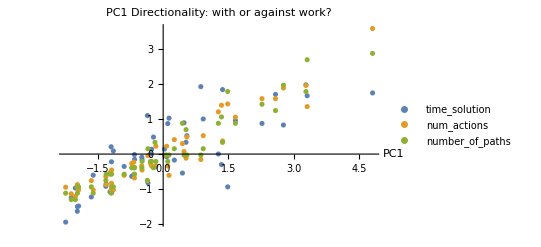

```mathematica
ListPlot[{workPCA[[1]],Standardize[#]}ᵀ&/@(workMatrixᵀ),AxesLabel->{"PC1", None},PlotLegends->{"time_solution","num_actions","number_of_paths"},PlotLabel->"PC1 Directionality: with or against work?"]
```

```mathematica
work=(Sign@SpearmanRho[workPCA[[1]],workMatrix[[;;,1]]])workPCA[[1]];
```

```mathematica
dataSolved=Append[dataSolvedᵀ,"work"->work]ᵀ;
labels=dataSolved//Keys//Normal//First;
```

## Export data

```mathematica
exportable=Prepend[Normal@Values@dataSolved,labels];
Export["data\\ttt_data.csv",exportable]
```

data\ttt_data.csv

## Self-avoidance correlations

```mathematica
<<Scatter`
```

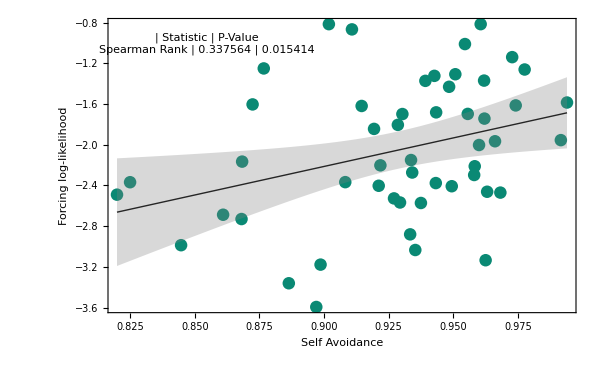

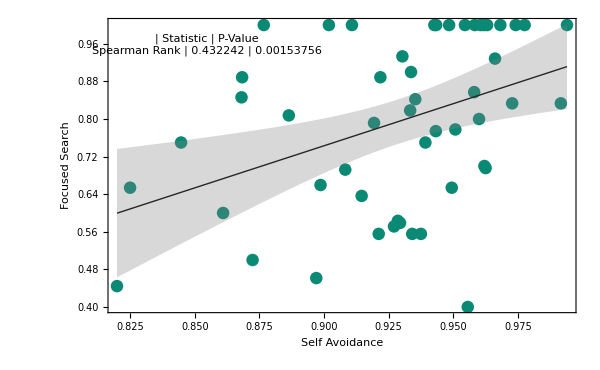

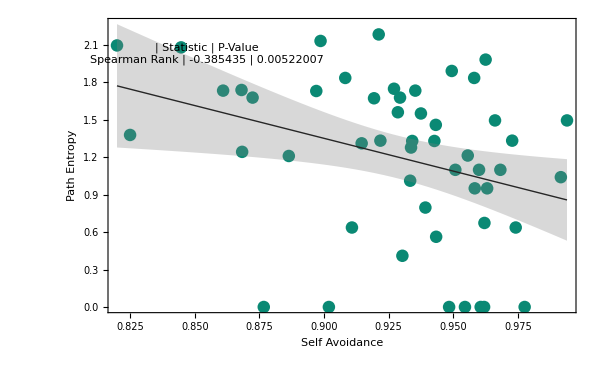

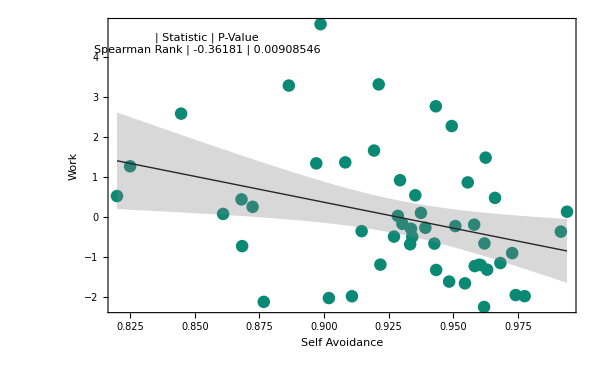

```mathematica
Scatter[(Normal@dataSolved[[;;,#]]&/@{"self avoidance","blocking"})ᵀ,{"Self Avoidance","Forcing log-likelihood"},ShowLabel->False]
Scatter[(Normal@dataSolved[[;;,#]]&/@{"self avoidance","shutter_zero_percent"})ᵀ,{"Self Avoidance","Focused Search"},ShowLabel->False]
Scatter[(Normal@dataSolved[[;;,#]]&/@{"self avoidance","first_moves_entropy"})ᵀ,{"Self Avoidance","Path Entropy"},ShowLabel->False]
Scatter[(Normal@dataSolved[[;;,#]]&/@{"self avoidance","work"})ᵀ,{"Self Avoidance","Work"},ShowLabel->False]
```